-2 a+5 a x^2+x^3-3 a x^3+a x^4

-3/5-(311 a)/420

-252/311

-252/311 (-2+x) (-1+x)

-252/311 (-2+x) (-1+x)+x

3.60756 BesselJ[1,x]+0.75229 BesselY[1,x]

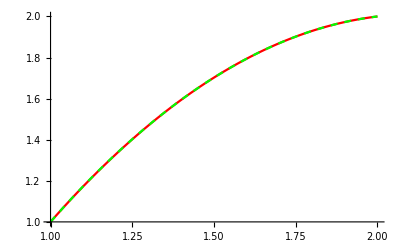

```mathematica
ϕ[x_]=(x−2)(x−1);
v[x_]=a ϕ[x];
u[x_]=v[x]+x;
eq[x_]=x ^2  D[u[x],{x,2}]+x D[u[x],x]+(x^2-1) u[x]//Expand
sol=Integrate[eq[x] ϕ[x], {x,1,2}]
na=Solve[sol==0,a][[1,1,2]]
nv[x_]=na ϕ[x]
nu[x_]=nv[x]+x

r[x_]=3.60756 BesselJ[1,x]+0.75229 BesselY[1,x]
Plot[{nu[x],r[x]},{x,1,2},PlotStyle->{{Red},{Dashed,Green}}]
```